```mathematica
<<mf25.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

recipJ[n_,m_,X_]:=Collect[Normal[InverseSeries[ex[n,m,x],X]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
fλNew3[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{X,0,n}],X];
Return[answer]]
```

#### The weight of f_λ at Hecke rank m is determined in Theorem 7 of Berndt in my paper; it has weight 4/(m-2). With outer exponent in Theorem 8 (my draft) altered from 1/(m-2) to 1 as above, the weight is 4 for all m. (This is H_{λ,4,m}, item 2 of my paper’s definition 7.)The cube (below: fλcubed) has weight 12. It is the numerator in the definition of item 3 of definition 9 in my paper. The denominator is J_m, weight zero, so the cusp form diamondCuspFrm defined below has weight 12.

```mathematica
(*  *)
fλcubed[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^3,{X,0,n}],X];
Return[answer]]
```

```mathematica
diamondCuspFrm[n_,m_,X_]:=
Collect[fλcubed[n,m,X]*recipJ[n,m,X],X]
```

```mathematica
Print[diamondCuspFrm[6,3,X]]
```

X-X^2/72+(7 X^3)/82944-(23 X^4)/80621568+(805 X^5)/1486016741376-(7 X^6)/17832200896512-(17357786380025 X^7)/92442129447518208-(914340879836245 X^8)/19967499960663932928-(98097607881457445 X^9)/30670079939579800977408-(3572540741339744345 X^10)/79496847203390844133441536-(7036935371751179195 X^11)/22895091994576563110431162368-(371440349809702285 X^12)/274741103934918757325173948416

```mathematica
srs=Normal[Series[diamondCuspFrm[10,3,x],{x,0,10}]];
c1=Coefficient[srs,x,1];
series=Collect[srs/c1,x];
Print[srs];
Print[series]
```

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

```mathematica
stream=OpenWrite["run24apr21no1"];
For[m=2,m<300,m++;
srs=Normal[Series[diamondCuspFrm[100,m,x],{x,0,100}]];
Write[stream,{m,srs}]];
Close[stream]
```

run24apr21no1

#### Dividing by J - constant introduces no singularities except at the constant, and they have weight zero and transform like γ = 1. Formally, the q_m - series for 1/(J_m - constant) introduces no singularities at all . Also note that f is in M (λ, k, -1) = > f^2 is in M (λ, 2 k, +1) . Hence in Berndt' s theorem 7 (my draft numbering) f_i^2 is in M (λ, 4m/(m - 2), +1) and f_i^(2m - 4) is in M (λ, 4m, +1) . So (for m = 3) f_i^2 is in M (λ, 12, +1) and so (for m = 3 again) f_i^2/J_ 3 should be a weight 12 cusp form .

```mathematica
fi[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^(1/(m-2)),{x,0,n}];
Return[answer]]
```

```mathematica
fiNo2[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Normal[Series[(numerator/denominator),{x,0,n}]];
Return[answer]]
```

```mathematica
fiNo3[n_,m_,x_]:=
Module[{kay,answer1,answer2,djaydx,oneovrjayminus1},
kay=K[n+1,m,x];
djaydx=-D[kay,x]/kay^2;
oneovrjayminus1=1+1/(kay-1);
answer1=x^m*djaydx^m*kay^(m-1)*oneovrjayminus1;
answer2=Normal[Series[answer1,{x,0,n}]];
Return[answer2]]
```

```mathematica
fiNoOuterExponent[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator),{x,0,n}];
Return[answer]]
```

```mathematica
fiWt6[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
power=3/m;
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^power,{x,0,n}];
Return[answer]]
```

```mathematica
stream=OpenWrite["run24apr21no1"];
For[m=2,m<300,m++;
srs=Normal[Series[diamondCuspFrm[100,m,x],{x,0,100}]];
Write[stream,{m,srs}]];
Close[stream]
```

run24apr21no1

#### Conjecture 6, clause 1:

```mathematica
f=diamondCuspFrm[10,3,x];
f=f/.x->2^6*3^3*x;
f=Collect[f/1728,x];
Print[f]
```

x-24 x^2+252 x^3-1472 x^4+4830 x^5-6048 x^6-16744 x^7+84480 x^8-113643 x^9-115920 x^10-34058364214245581228176080 x^11-15206392746927044852432526720 x^12-1913015129654100105184110541200 x^13-46701327962212432285936753304640 x^14-553217230896477645253245466055040 x^15-4137993103417587454942081944656640 x^16-22630263274602587503526506735831920 x^17-98611068710272421765657800389132720 x^18-360588111176464359865167952055723040 x^19-1162725068252312100448288098224140800 x^20

```mathematica
data={};
f=diamondCuspFrm[100,3,x];
f=f/.x->2^6*3^3*x;
f=Collect[f/1728,x];
For[k=0,k<100,k++;
cf=Coefficient[f,x,k];
AppendTo[data,cf-RamanujanTau[k]]];
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Conjecture 6, clause 2:

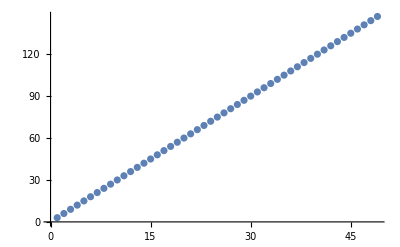

{{1,3},{2,6},{3,9},{4,12},{5,15},{6,18},{7,21},{8,24},{9,27},{10,30},{11,33},{12,36},{13,39},{14,42},{15,45},{16,48},{17,51},{18,54},{19,57},{20,60},{21,63},{22,66},{23,69},{24,72},{25,75},{26,78},{27,81},{28,84},{29,87},{30,90},{31,93},{32,96},{33,99},{34,102},{35,105},{36,108},{37,111},{38,114},{39,117},{40,120},{41,123},{42,126},{43,129},{44,132},{45,135},{46,138},{47,141},{48,144},{49,147}}

run27jul21no2

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run27jul21no2"];

degrees={};
For[n=0,n<49,n++;
data={};
For[k=2,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
(* Delta_12^diamond!: Df. 9.4 in the interpolations paper*)
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

#### Conjecture 6, clause 3:

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
AppendTo[data,Length[fim]]];
Print[data]
```

{3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
AppendTo[data,fim[[1,1]]/64-RamanujanTau[n]*(-1)^(n+1)]];
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
Print[{k,n,fim}]]
```

{1,1,{{64,1},{1,1},{x,3}}}

{2,2,{{1536,1},{1,1},{x,4},{-28/3+x^2,1}}}

{3,3,{{16128,1},{1,1},{x,5},{7792/63-(1432 x^2)/63+x^4,1}}}

{4,4,{{94208,1},{1,-1},{1,1},{x,6},{-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6,1}}}

{5,5,{{309120,1},{1,-1},{1,1},{x,7},{895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8,1}}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<5,k++;
Print["----------------------------------------------------"];
n=list[[k,1]];
Print["n: ",n];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
Print[fim];
lf=Last[fim];
Print[lf];
Print[lf[[2]]]]
```

----------------------------------------------------

n: 1

{{64,1},{1,1},{x,3}}

{x,3}

3

----------------------------------------------------

n: 2

{{1536,1},{1,1},{x,4},{-28/3+x^2,1}}

{-28/3+x^2,1}

1

----------------------------------------------------

n: 3

{{16128,1},{1,1},{x,5},{7792/63-(1432 x^2)/63+x^4,1}}

{7792/63-(1432 x^2)/63+x^4,1}

1

----------------------------------------------------

n: 4

{{94208,1},{1,-1},{1,1},{x,6},{-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6,1}}

{-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6,1}

1

----------------------------------------------------

n: 5

{{309120,1},{1,-1},{1,1},{x,7},{895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8,1}}

{895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8,1}

1

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];

lf=Last[fim];

AppendTo[data,lf[[2]]]];
Print[data]
```

{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=1,k<5,k++;
Print["n:  ",n];
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
lf=Last[fim];
Print[lf];
AppendTo[data,{n,IrreduciblePolynomialQ[lf[[1]]]}]];
Print[data]
```

n:  9

{-28/3+x^2,1}

n:  2

{7792/63-(1432 x^2)/63+x^4,1}

n:  3

{-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6,1}

n:  4

{895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8,1}

{{2,True},{3,True},{4,True},{5,True}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=1,k<Length[list],k++;

n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
lf=Last[fim];

AppendTo[data,{n,IrreduciblePolynomialQ[lf[[1]]]}]];
Print[data]
```

{{2,True},{3,True},{4,True},{5,True},{6,True},{7,True},{8,True},{9,True},{10,True},{11,True},{12,True},{13,True},{14,True},{15,True},{16,True},{17,True},{18,True},{19,True},{20,True},{21,True},{22,True},{23,True},{24,True},{25,True},{26,True},{27,True},{28,True},{29,True},{30,True},{31,True},{32,True},{33,True},{34,True},{35,True},{36,True},{37,True},{38,True},{39,True},{40,True},{41,True},{42,True},{43,True},{44,True},{45,True},{46,True},{47,True},{48,True},{49,True}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
lf=Length[fim];
AppendTo[data,lf]];
Print[data]
```

{3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
numericalterms={};
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
Print[{n,fim[[2]]}]]
```

{1,{1,1}}

{2,{1,1}}

{3,{1,1}}

{4,{1,-1}}

{5,{1,-1}}

{6,{1,-1}}

{7,{1,1}}

{8,{1,1}}

{9,{1,1}}

{10,{1,1}}

{11,{1,1}}

{12,{1,1}}

{13,{1,1}}

{14,{1,1}}

{15,{1,1}}

{16,{1,1}}

{17,{1,1}}

{18,{1,1}}

{19,{1,1}}

{20,{1,1}}

{21,{1,1}}

{22,{1,1}}

{23,{1,1}}

{24,{1,1}}

{25,{1,1}}

{26,{1,1}}

{27,{1,1}}

{28,{1,1}}

{29,{1,1}}

{30,{1,1}}

{31,{1,1}}

{32,{1,1}}

{33,{1,1}}

{34,{1,1}}

{35,{1,1}}

{36,{1,1}}

{37,{1,1}}

{38,{1,1}}

{39,{1,1}}

{40,{1,1}}

{41,{1,1}}

{42,{1,1}}

{43,{1,1}}

{44,{1,1}}

{45,{1,1}}

{46,{1,1}}

{47,{1,1}}

{48,{1,1}}

{49,{1,1}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data2={};
data3={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
rem2=Remainder[poly,x^(n+2)];
rem3=Remainder[poly,x^(n+3)];
If[rem2!=0,AppendTo[data2,n]];
If[rem3==0,AppendTo[data3,n]]];
Print[data2];Print[data3]
```

{}

{}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
numericalterms={};
numerators={};
denominators={};
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
Print[fim]]
```

{{64,1},{1,1},{x,3}}

{{1536,1},{1,1},{x,4},{-28/3+x^2,1}}

{{16128,1},{1,1},{x,5},{7792/63-(1432 x^2)/63+x^4,1}}

{{94208,1},{1,-1},{1,1},{x,6},{-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6,1}}

{{309120,1},{1,-1},{1,1},{x,7},{895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8,1}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
numericalterms={};
numerators={};
denominators={};
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
last=Last[fim][[1]];
degree=Exponent[last,x];
Print[last," ",degree]]
```

x 1

-28/3+x^2 2

7792/63-(1432 x^2)/63+x^4 4

-1454144/621+(348400 x^2)/621-(26348 x^4)/621+x^6 6

895148288/13041-(250721536 x^2)/13041+(3517856 x^4)/1863-(328688 x^6)/4347+x^8 8

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
fim=factorIntoIrreducibleMonics[poly];
last=Last[fim][[1]];
degree=Exponent[last,x];
AppendTo[data,{n,degree}]];
Print[data]
```

{{1,1},{2,2},{3,4},{4,6},{5,8},{6,10},{7,12},{8,14},{9,16},{10,18},{11,20},{12,22},{13,24},{14,26},{15,28},{16,30},{17,32},{18,34},{19,36},{20,38},{21,40},{22,42},{23,44},{24,46},{25,48},{26,50},{27,52},{28,54},{29,56},{30,58},{31,60},{32,62},{33,64},{34,66},{35,68},{36,70},{37,72},{38,74},{39,76},{40,78},{41,80},{42,82},{43,84},{44,86},{45,88},{46,90},{47,92},{48,94},{49,96}}

```mathematica
stream=OpenRead["run27jul21no2"];
list=ReadList[stream];
Close[stream];
data={};
short={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
last=Last[fim][[1]];
degree=Exponent[last,x];
lf=Length[fim];
If[lf<3,AppendTo[short,{n,poly}]];
If[lf>2,
AppendTo[data,degree-(2*n-2)]]];
Print[data];
Print[short]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{}